# Лабораторная работа № 2. Избранные свойства чисел и их последовательностей. Часть 1.

Выполнила студентка ММФ БГУ 
КМ, 1 к, 5 гр. Бельская Е.А.
    2 сентября 2019

## 1. Золотое сечение.

Золотое сечение определяют следующим образом. Пусть заданы две величины a и b, a>b. Отношение a/b - золотое сечение,  если выполнено следующее соотношение a/b=(a+b)/a. Золотое сечение - уникальное число: оно встречается в различных сферах жизни, от биологии до государственных флагов различных стран.  Попробуйте получить золотое сечение различными способами.

### 1.1 Квадратное уравнение.

Если в соотношении a/b=(a+b)/a выполнить небольшое преобразование в правой части, получим ему эквивалентное: a/b=1+b/a.  Проделав замену a/b=x,  получим уравнение x=1+1/x. Положительное решение этого уравнения представляет собой точное значение золотого сечения. Используя возможности пакета Mathematica найдём его.

1.1 .1 Внимательно изучите приведённую последовательность команд. Особое внимание уделите встроенным функциям.

```mathematica
ClearAll[a,b,x]
```

```mathematica
a/b==(a+b)/a
```

a/b==(a+b)/a

```mathematica
a/b==(a+b)/a//Apart
```

a/b==1+b/a

```mathematica
Eliminate[{a/b==(a+b)/a,x==a/b},{a,b}]
```

-x+x^2==1

```mathematica
Solve[%]
```

{{x→1/2 (1-√5)},{x→1/2 (1+√5)}}

```mathematica
myRatio=x/.(a/b==(a+b)/a//Eliminate[{#,x==a/b},{a,b}]&//Solve[#&&x>0,x]&)//First
```

1/2 (1+√5)

### 1.2 Цепная дробь.

Обратите внимание на вид уравнения из предыдущего пункта: x=1+1/x. Попробуем заменить x в правой части, на правую часть - ведь она равна x. Получим x=1+1/(1+1/x), заменяя аналогичным образом бесконечное число раз, выразим золотое сечение через так называемую цепную дробь: x=1+1/(1+1/(1+1/(1+1/(...))))

1.2 .1 Получите значение золотого сечения с различной точностью. Используя формулу цепной дроби. 
1.2.2* Используя механизм цепных дробей (изучите его самостоятельно) получите приближение для числа π.

```mathematica
f[1]:=1
```

```mathematica
f[n_]:=1+1/f[n-1]
```

```mathematica
f[#]&/@Range[20]//N
```

{1.,2.,1.5,1.66667,1.6,1.625,1.61538,1.61905,1.61765,1.61818,1.61798,1.61806,1.61803,1.61804,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803}

```mathematica
pi1[n_]:=(2n+1)^2
```

```mathematica
pi[n_,0]:=1
```

```mathematica
pi[n_,m_]:=2+pi1[n+1]/pi[n+1,m-1]
```

```mathematica
4/(1+1/pi[0,#])&/@Range[1,200]//N
```

{3.66667,2.8,3.39524,2.93968,3.30938,2.99802,3.26707,3.03014,3.24184,3.0505,3.22507,3.06456,3.21311,3.07485,3.20415,3.08272,3.19719,3.08892,3.19162,3.09395,3.18707,3.09809,3.18328,3.10158,3.18007,3.10454,3.17732,3.1071,3.17494,3.10933,3.17285,3.11128,3.17101,3.11302,3.16938,3.11456,3.16791,3.11595,3.1666,3.1172,3.16541,3.11833,3.16432,3.11937,3.16333,3.12031,3.16243,3.12118,3.16159,3.12198,3.16083,3.12272,3.16011,3.12341,3.15945,3.12405,3.15884,3.12464,3.15826,3.1252,3.15772,3.12572,3.15722,3.12621,3.15675,3.12667,3.1563,3.1271,3.15588,3.12751,3.15548,3.12789,3.15511,3.12826,3.15475,3.12861,3.15441,3.12893,3.15409,3.12925,3.15379,3.12954,3.1535,3.12983,3.15322,3.1301,3.15296,3.13036,3.1527,3.1306,3.15246,3.13084,3.15223,3.13107,3.15201,3.13128,3.1518,3.13149,3.15159,3.13169,3.1514,3.13188,3.15121,3.13207,3.15103,3.13225,3.15085,3.13242,3.15068,3.13258,3.15052,3.13274,3.15036,3.1329,3.15021,3.13305,3.15007,3.13319,3.14993,3.13333,3.14979,3.13346,3.14966,3.13359,3.14953,3.13372,3.14941,3.13384,3.14929,3.13396,3.14917,3.13407,3.14906,3.13419,3.14895,3.13429,3.14884,3.1344,3.14874,3.1345,3.14863,3.1346,3.14854,3.1347,3.14844,3.13479,3.14835,3.13488,3.14826,3.13497,3.14817,3.13506,3.14809,3.13514,3.148,3.13522,3.14792,3.1353,3.14784,3.13538,3.14777,3.13546,3.14769,3.13553,3.14762,3.1356,3.14755,3.13568,3.14748,3.13574,3.14741,3.13581,3.14734,3.13588,3.14727,3.13594,3.14721,3.13601,3.14715,3.13607,3.14709,3.13613,3.14703,3.13619,3.14697,3.13625,3.14691,3.1363,3.14686,3.13636,3.1468,3.13641,3.14675,3.13646,3.14669,3.13652,3.14664,3.13657,3.14659,3.13662}

### 1.3. Соотношение с радикалом.

1.3 .1 Получите значение золотого сечения с различной точностью. Используя данное радикальное соотношение.

```mathematica
fr[1]:=1
```

```mathematica
fr[n_]:=Sqrt[1+fr[n-1]]
```

```mathematica
fr[#]&/@Range[20]//N
```

{1.,1.41421,1.55377,1.59805,1.61185,1.61612,1.61744,1.61785,1.61798,1.61802,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803}

### 1.4 Связь с числами Фибоначчи

1.4 .1 Получите значение золотого сечения с различной точностью. Используя связь с последовательностью Фибоначчи.

```mathematica
fib[1]:=1
fib[2]:=1
```

```mathematica
fib[n_]:=fib[n-1]+fib[n-2]
```

```mathematica
fib1[n_]:=fib[n+1]/fib[n]
```

```mathematica
fib1[#]&/@Range[20]//N
```

{1.,2.,1.5,1.66667,1.6,1.625,1.61538,1.61905,1.61765,1.61818,1.61798,1.61806,1.61803,1.61804,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803}

### 1.5 Немного геометрии.

1.5 .1 Изобразите несколько отсечений вручную, как показано выше. 
  1.5 .2 Реализуйте функцию, которая делает произвольное количество отсечений квадрата от некоторого "золотого" прямоугольника.
  1.5 .3* Реализуйте функцию, которая делает произвольное количество отсечений квадрата от некоторого "золотого" прямоугольника, меняя при этом цвет при каждом отсечении.

```mathematica
b=5;
```

```mathematica
a=5*myRatio;
```

```mathematica
a/b
```

1/2 (1+√5)

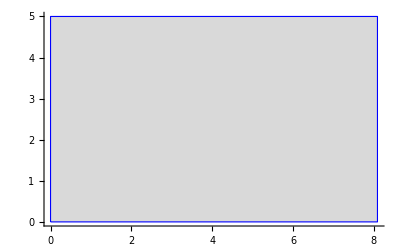

```mathematica
Graphics[{LightGray,EdgeForm[{Thick,Blue}],Rectangle[{0,0},{0+a,0+b}]},Axes->True,ImageSize->400]
```

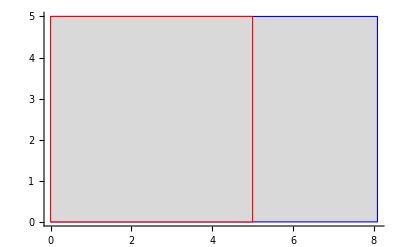

```mathematica
Graphics[{LightGray,EdgeForm[{Thick,Blue}],Rectangle[{0,0},{0+a,0+b}],EdgeForm[{Thick,Red}],Rectangle[{0,0},{0+b,0+b}]},Axes->True,ImageSize->400]
```

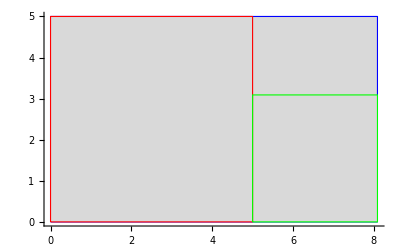

```mathematica
Graphics[{LightGray,EdgeForm[{Thick,Blue}],Rectangle[{0,0},{0+a,0+b}],EdgeForm[{Thick,Red}],Rectangle[{0,0},{0+b,0+b}],EdgeForm[{Thick,Green}],Rectangle[{b,0},{a,a-b}]},Axes->True,ImageSize->400]
```

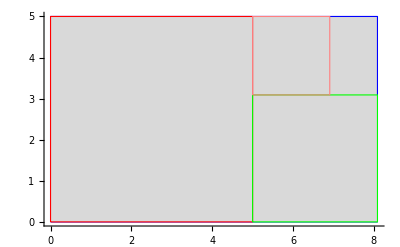

```mathematica
Graphics[{LightGray,EdgeForm[{Thick,Blue}],Rectangle[{0,0},{0+a,0+b}],EdgeForm[{Thick,Red}],Rectangle[{0,0},{0+b,0+b}],EdgeForm[{Thick,Green}],Rectangle[{b,0},{a,a-b}], EdgeForm[{Thick,Pink}],Rectangle[{b,a-b},{3b-a,b}]},Axes->True,ImageSize->400]
```

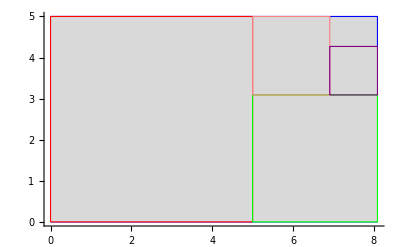

```mathematica
Graphics[{LightGray,EdgeForm[{Thick,Blue}],Rectangle[{0,0},{0+a,0+b}],EdgeForm[{Thick,Red}],Rectangle[{0,0},{0+b,0+b}],EdgeForm[{Thick,Green}],Rectangle[{b,0},{a,a-b}], EdgeForm[{Thick,Pink}],Rectangle[{b,a-b},{3b-a,b}], EdgeForm[{Thick,Purple}],Rectangle[{3b-a, a-b},{a,3a-4b}]},Axes->True,ImageSize->400]
```

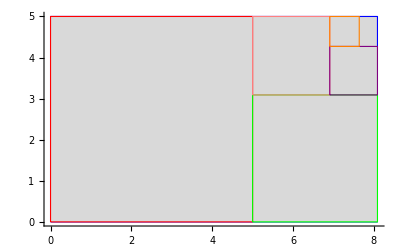

```mathematica
Graphics[{LightGray,EdgeForm[{Thick,Blue}],Rectangle[{0,0},{0+a,0+b}],EdgeForm[{Thick,Red}],Rectangle[{0,0},{0+b,0+b}],EdgeForm[{Thick,Green}],Rectangle[{b,0},{a,a-b}], EdgeForm[{Thick,Pink}],Rectangle[{b,a-b},{3b-a,b}], EdgeForm[{Thick,Purple}],Rectangle[{3b-a, a-b},{a,3a-4b}],  EdgeForm[{Thick,Orange}],Rectangle[{3b-a, 3a-4b},{8b-4a,b}]},Axes->True,ImageSize->400]
```

```mathematica
gr[0]:={{0,0},{1,-1}};
gr[n_]:=Module[{ϕ=GoldenRatio,m=Mod[n,4],a,b,c,d},{{a,b},{c,d}}=gr[n-1];
Switch[Mod[n,4],0,{{a,d},{a+ϕ^-n,d-ϕ^-n}},1,{{c,d+ϕ^-n},{c+ϕ^-n,d}},2,{{c-ϕ^-n,b+ϕ^-n},{c,b}},3,{{a-ϕ^-n,b},{a,b-ϕ^-n}}]];
```

```mathematica
fun[p_]:=Graphics[{ LightGray,EdgeForm[{Thick,Black}],Rectangle[{0,0},{GoldenRatio,-1}],EdgeForm[{Thick,Black}],Table[{ColorData[34,k+1],Rectangle@@gr[k]},{k,0,p-1}]}]
```

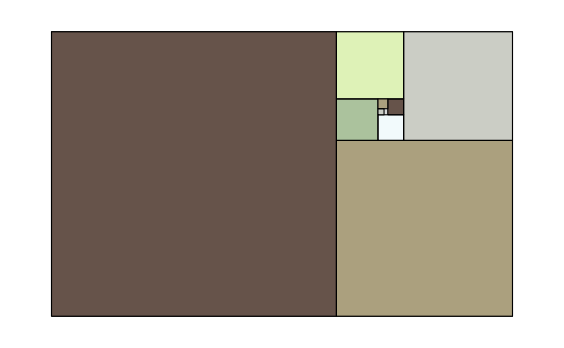

```mathematica
fun[9]
```

```mathematica
f[{a_,b_}]:=If[a>b, {a-b,b},{a,b-a}]
```

```mathematica
f[{a,b}]
```

{-5+5/2 (1+√5),5}

```mathematica
NestList[f,{a,b} ,10]
```

{{5/2 (1+√5),5},{-5+5/2 (1+√5),5},{-5+5/2 (1+√5),10-5/2 (1+√5)},{-15+5 (1+√5),10-5/2 (1+√5)},{-15+5 (1+√5),25-15/2 (1+√5)},{-40+25/2 (1+√5),25-15/2 (1+√5)},{-40+25/2 (1+√5),65-20 (1+√5)},{-105+65/2 (1+√5),65-20 (1+√5)},{-105+65/2 (1+√5),170-105/2 (1+√5)},{-275+85 (1+√5),170-105/2 (1+√5)},{-275+85 (1+√5),445-275/2 (1+√5)}}

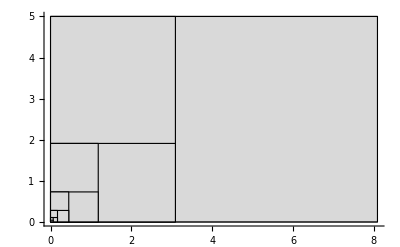

```mathematica
Graphics[{LightGray,EdgeForm[{Thick,Black}],Rectangle[{0,0},{0+a,0+b}], Rectangle[{0,0},{0,0}+(#)]&/@NestList[f,{a,b} ,10]},Axes->True,ImageSize->400]
```

```mathematica
rec[n_]:=Graphics[{LightGray,EdgeForm[{Thick,Black}],Rectangle[{0,0},{0+a,0+b}], {RandomColor[],Rectangle[{0,0},{0,0}+(#)]}&/@NestList[f,{a,b} ,n]},Axes->True,ImageSize->400]
```

```mathematica
rec[11]
```

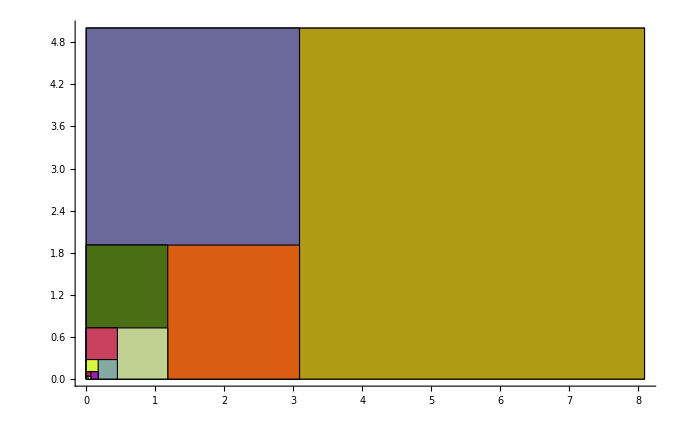

## 2. Числа Софи Жермен

2.1 Реализуйте функцию, которая находит все числа Софи - Жермен в заданном промежутке.
   2.2 Оцените скорость работы функции на различных выборках данных. Прокомментируйте. 
   2.3 Порассуждайте о вопросе количества чисел Софи Жермен. Бесконечно ли их множество на ваш взгляд?

```mathematica
SGQ[p_]:=PrimeQ[p]===PrimeQ[2p+1]===True
```

```mathematica
myFunc[m_,n_]:=Select[Range[m,n],SGQ]
```

```mathematica
myFunc[1,1000]
```

{2,3,5,11,23,29,41,53,83,89,113,131,173,179,191,233,239,251,281,293,359,419,431,443,491,509,593,641,653,659,683,719,743,761,809,911,953}

```mathematica
Timing[myFunc[1,10000]]
```

{0.03125,{2,3,5,11,23,29,41,53,83,89,113,131,173,179,191,233,239,251,281,293,359,419,431,443,491,509,593,641,653,659,683,719,743,761,809,911,953,1013,1019,1031,1049,1103,1223,1229,1289,1409,1439,1451,1481,1499,1511,1559,1583,1601,1733,1811,1889,1901,1931,1973,2003,2039,2063,2069,2129,2141,2273,2339,2351,2393,2399,2459,2543,2549,2693,2699,2741,2753,2819,2903,2939,2963,2969,3023,3299,3329,3359,3389,3413,3449,3491,3539,3593,3623,3761,3779,3803,3821,3851,3863,3911,4019,4073,4211,4271,4349,4373,4391,4409,4481,4733,4793,4871,4919,4943,5003,5039,5051,5081,5171,5231,5279,5303,5333,5399,5441,5501,5639,5711,5741,5849,5903,6053,6101,6113,6131,6173,6263,6269,6323,6329,6449,6491,6521,6551,6563,6581,6761,6899,6983,7043,7079,7103,7121,7151,7193,7211,7349,7433,7541,7643,7649,7691,7823,7841,7883,7901,8069,8093,8111,8243,8273,8513,8663,8693,8741,8951,8969,9029,9059,9221,9293,9371,9419,9473,9479,9539,9629,9689,9791}}

```mathematica
Timing[myFunc[1,15000]]
```

{0.03125,{2,3,5,11,23,29,41,53,83,89,113,131,173,179,191,233,239,251,281,293,359,419,431,443,491,509,593,641,653,659,683,719,743,761,809,911,953,1013,1019,1031,1049,1103,1223,1229,1289,1409,1439,1451,1481,1499,1511,1559,1583,1601,1733,1811,1889,1901,1931,1973,2003,2039,2063,2069,2129,2141,2273,2339,2351,2393,2399,2459,2543,2549,2693,2699,2741,2753,2819,2903,2939,2963,2969,3023,3299,3329,3359,3389,3413,3449,3491,3539,3593,3623,3761,3779,3803,3821,3851,3863,3911,4019,4073,4211,4271,4349,4373,4391,4409,4481,4733,4793,4871,4919,4943,5003,5039,5051,5081,5171,5231,5279,5303,5333,5399,5441,5501,5639,5711,5741,5849,5903,6053,6101,6113,6131,6173,6263,6269,6323,6329,6449,6491,6521,6551,6563,6581,6761,6899,6983,7043,7079,7103,7121,7151,7193,7211,7349,7433,7541,7643,7649,7691,7823,7841,7883,7901,8069,8093,8111,8243,8273,8513,8663,8693,8741,8951,8969,9029,9059,9221,9293,9371,9419,9473,9479,9539,9629,9689,9791,10061,10091,10163,10253,10271,10313,10331,10529,10589,10613,10691,10709,10733,10781,10799,10883,11171,11321,11369,11393,11471,11519,11549,11579,11699,11783,11801,11813,11831,11909,11939,12011,12041,12101,12119,12203,12263,12329,12653,12671,12791,12821,12899,12923,12959,13001,13049,13229,13313,13451,13463,13553,13619,13649,13763,13883,13901,13913,14009,14081,14153,14159,14249,14303,14321,14489,14561,14621,14669,14699,14741,14783,14831,14879,14939}}

```mathematica
Which[PrimeQ[#]&&PrimeQ[2#+1],#]&/@Range[200]//DeleteCases[#,Null]&
```

{2,3,5,11,23,29,41,53,83,89,113,131,173,179,191}

## 3. Числа палиндромы

3.1 Реализуйте булеву функцию - критерий, которая позволяет определить будет ли заданное число палиндромом.

```mathematica
paliQ[n_]:=IntegerDigits[n]===Reverse@IntegerDigits[n]
paliQ[123]
```

False

```mathematica
paliQ[12321]
```

True

# Лабораторная работа № 3. Избранные свойства чисел и их последовательностей. Часть 2.

## 1. Простые числа

### Критерий простоты числа.

Простейший тест простоты числа выглядит следующим образом.
Пусть на входе есть некоторое натуральное число p.
Проверяем число p на делимость на числа от 2 до [√p], если делителей не найдено, то число простое.

1.1. Реализуйте указанный тест простоты числа.

```mathematica
fp[p_]:=If[DivisorSum[p, #&, (#≥2)&&(#≤Sqrt[p])&]==0, True, False]
```

```mathematica
Timing[fp[994]]
```

{0.,False}

### Решето Эратосфена

```mathematica
l1=Range[2,50]
```

{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}

```mathematica
div[x_,y_]:=(Mod[x,y]==0)===x>y===True
```

```mathematica
If[div[#,2],Style[#,Green],#]&/@l1
```

{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}

```mathematica
l2=If[div[#,2],Null,#]&/@l1//DeleteCases[#,Null]&
```

{2,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49}

```mathematica
If[div[#,3],Style[#,Green],#]&/@l2
```

{2,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49}

```mathematica
l3=If[div[#,3],Null,#]&/@l2//DeleteCases[#,Null]&
```

{2,3,5,7,11,13,17,19,23,25,29,31,35,37,41,43,47,49}

```mathematica
If[div[#,5],Style[#,Green],#]&/@l3
```

{2,3,5,7,11,13,17,19,23,25,29,31,35,37,41,43,47,49}

```mathematica
l4=If[div[#,5],Null,#]&/@l3//DeleteCases[#,Null]&
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,49}

```mathematica
If[div[#,7],Style[#,Green],#]&/@l4
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,49}

```mathematica
l5=If[div[#,7],Null,#]&/@l4//DeleteCases[#,Null]&
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47}

### Простые числа близнецы.

```mathematica
tp[m_,n_]:=Block[{list},list=Select[Range[m,n],PrimeQ[#]&&NextPrime[#]==2+#&];
Join[list,(#+2)&/@list]//Sort//Partition[#,2]&]
```

```mathematica
tp[1,20]
```

{{3,5},{5,7},{11,13},{17,19}}

### Арифметическая прогрессия из простых чисел.

```mathematica
pr=Array[Prime,50]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229}

```mathematica
list={}
```

{}

```mathematica
If[pr[[#+1]]-pr[[#]]==pr[[#+2]]-pr[[#+1]],Join[list,{pr[[#]],pr[[#+1]],pr[[#+2]]}]]&/@Range[48]//DeleteCases[#,Null]&
```

{{3,5,7},{47,53,59},{151,157,163},{167,173,179},{199,211,223}}

## 2. Числа Мерсенна

```mathematica
mf[n_]:=2^n-1
```

```mathematica
mf1[m_]:=DeleteCases[If[PrimeQ[mf[#]],2^#-1]&/@Range[m],Null]
```

```mathematica
mf1[50]
```

{3,7,31,127,8191,131071,524287,2147483647}

## 3. Алгоритм Гаусса вычисления даты Пасхи

```mathematica
year[n_]:= Module[{d=Mod[19Mod[n,19]+15,30],e=Mod[2 Mod[n,4]+ 4Mod[n,7]+6Mod[19Mod[n,19]+15,30]+6,7]},If[ d +e≤26,  Print[4+e+d," апреля"],Print[e+d-26, " мая"]]]
```

```mathematica
year[2022]
```

24 апреля